```mathematica
(*format intended for easy use with event data from multiple trials*)
```

```mathematica
OlaparibEvents=Import[NotebookDirectory[]<>"Olaparib_events.csv","CSV"];
ChemotherapyEvents=Import[NotebookDirectory[]<>"Paclitaxel_Carboplatin_events.csv","CSV"];
```

```mathematica
MySurvivalFunction[β_,α_,t_]:=1-CDF[WeibullDistribution[α,β],t]
MySurvivalFunctionInverse[β_,α_,pfs_]:=InverseCDF[WeibullDistribution[α,β],pfs]
MyProbabilityFunction[β_,α_,t_]:=PDF[WeibullDistribution[α,β],t]

EvaluateDataLikelihood[events_,β_,α_]:=Module[{},
progressionevents=Select[events,#⟦2⟧==0&]⟦All,1⟧;
censoringevents=Select[events,#⟦2⟧==1&]⟦All,1⟧;

LikelihoodOfProgressionEvents=Product[MyProbabilityFunction[β,α,progressionevents⟦i⟧],{i,1,Length[progressionevents]}];
LikelihoodOfCensoringEvents=Product[MySurvivalFunction[β,α,censoringevents⟦i⟧],{i,1,Length[censoringevents]}];

If[LikelihoodOfProgressionEvents<0,LikelihoodOfProgressionEvents==0];
If[LikelihoodOfCensoringEvents<0,LikelihoodOfCensoringEvents==0];

OverallLikelihood=LikelihoodOfProgressionEvents*LikelihoodOfCensoringEvents; 

If[OverallLikelihood==0,-1000,Log[10,OverallLikelihood]]
]
```

```mathematica
EvaluateDataLikelihood[OlaparibEvents⟦2;;⟧,1,0.1]
```

-73.5329

```mathematica
EvaluateDataLikelihood[OlaparibEvents⟦2;;⟧,1,1]
```

-180.71

```mathematica
TableOfLikelihoods=Table[{β,α,EvaluateDataLikelihood[OlaparibEvents⟦2;;⟧,β,α]},{β,1,30,0.5},{α,0.2,3,0.05}];
```

General::munfl: 8.92982×10^-56 2.75465×10^-258 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.77386×10^-60 6.88197×10^-295 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.09476×10^-83 6.46826×10^-254 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MaxLikelihood=Max[TableOfLikelihoods⟦All,All,3⟧]
```

-43.5605

```mathematica
TableOfLikelihoods⟦All,All,3⟧-MaxLikelihood;
```

```mathematica
AllBetaValues=TableOfLikelihoods⟦All,1,1⟧
AllAlphaValues=TableOfLikelihoods⟦1,All,2⟧
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.,26.5,27.,27.5,28.,28.5,29.,29.5,30.}

{0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.}

```mathematica
BetaValueTicks={Reverse[Range[Length[AllBetaValues]]],AllBetaValues}ᵀ⟦9;;-1;;10⟧
```

{{51,5.},{41,10.},{31,15.},{21,20.},{11,25.},{1,30.}}

```mathematica
AlphaValueTicks={Range[Length[AllAlphaValues]],AllAlphaValues}ᵀ⟦7;;-1;;10⟧

AlphaValueTicks={Range[Length[AllAlphaValues]],AllAlphaValues}ᵀ⟦17;;-1;;20⟧
```

{{7,0.5},{17,1.},{27,1.5},{37,2.},{47,2.5},{57,3.}}

{{17,1.},{37,2.},{57,3.}}

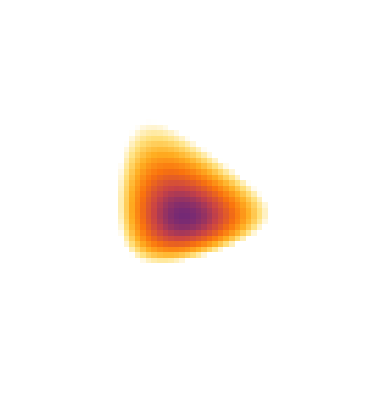

```mathematica
ParameterConfidencePlot=ArrayPlot[Reverse[TableOfLikelihoods⟦All,All,3⟧-MaxLikelihood],PlotRangePadding->None,ColorFunction->(ColorData["SunsetColors"][1-(#-Log[10,0.01])/2.5]&),ColorFunctionScaling->False,FrameTicks->{{(*vertical*)Table[{i⟦1⟧,i⟦2⟧,{0,0.02}},{i,Map[Round[#,1]&,BetaValueTicks]}],None},{(*x*)Table[{i⟦1⟧,NumberForm[i⟦2⟧,{2,0},NumberPoint->""],{0,0.02}},{i,AlphaValueTicks}],None}},BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],FrameLabel->{"Beta (scale)","Alpha (shape)"},ImagePadding->{{50,10},{50,10}},ImageSize->{{500},{180}}]
```

```mathematica
Export[NotebookDirectory[]<>"Parameter confidence interval plot.pdf",ParameterConfidencePlot,"PDF"]
Export[NotebookDirectory[]<>"Parameter confidence interval plot.png",ParameterConfidencePlot,"PNG",ImageResolution->600]
```

D:\Dropbox\_Grants\Cancer Research Institute Technology Impact Award\fitting events to log normal\Parameter confidence interval plot.pdf

D:\Dropbox\_Grants\Cancer Research Institute Technology Impact Award\fitting events to log normal\Parameter confidence interval plot.png

```mathematica
LikelihoodTicks={{21,0.01},{11,0.1},{1,1}};
```

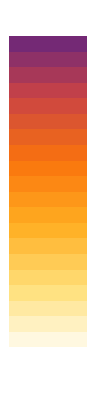

```mathematica
ArrayPlot[Table[{y,y,y,y,y},{y,0,-2,-0.1}],PlotRangePadding->None,ColorFunction->(ColorData["SunsetColors"][1-(#-Log[10,0.01])/2.5]&),ColorFunctionScaling->False,FrameTicks->{{(*vertical*)Table[{i⟦1⟧,i⟦2⟧,{0,0.02}},{i,LikelihoodTicks}],None},{(*x*)None,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],FrameLabel->{"Relative likelihood",},ImagePadding->{{50,10},{50,10}},ImageSize->{{500},{180}}]
```

```mathematica
LikelihoodTicks={{41,0.01},{21,0.1},{1,1}};
```

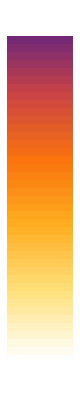

D:\Dropbox\_Grants\Cancer Research Institute Technology Impact Award\fitting events to log normal\Parameter confidence interval colorscale.pdf

D:\Dropbox\_Grants\Cancer Research Institute Technology Impact Award\fitting events to log normal\Parameter confidence interval colorscale.png

```mathematica
LikelihoodColorScale=ArrayPlot[Table[{y,y,y,y,y,y,y,y},{y,0,-2,-0.05}],PlotRangePadding->None,ColorFunction->(ColorData["SunsetColors"][1-(#-Log[10,0.01])/2.5]&),ColorFunctionScaling->False,FrameTicks->{{(*vertical*)Table[{i⟦1⟧,i⟦2⟧,{0,0.2}},{i,LikelihoodTicks}],None},{(*x*)None,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],FrameLabel->{"Relative likelihood",},ImagePadding->{{50,10},{50,10}},ImageSize->{{500},{180}}]

Export[NotebookDirectory[]<>"Parameter confidence interval colorscale.pdf",LikelihoodColorScale,"PDF"]
Export[NotebookDirectory[]<>"Parameter confidence interval colorscale.png",LikelihoodColorScale,"PNG",ImageResolution->600]
```

```mathematica
SortedLikelihoods=Sort[Flatten[TableOfLikelihoods,1],#1⟦3⟧>#2⟦3⟧&];
```

#### chemotherapy fit

```mathematica
TableOfLikelihoodsChemotherapy=Table[{β,α,EvaluateDataLikelihood[ChemotherapyEvents⟦2;;⟧,β,α]},{β,1,30,0.5},{α,0.2,3,0.05}];
```

General::munfl: 1.16331×10^-271 7.22758×10^-55 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.90854×10^-302 1.38911×10^-61 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.27797×10^-123 1.05194×10^-214 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
TableOfLikelihoods//Dimensions
```

{59,57,3}

```mathematica
SortedLikelihoods=Sort[Flatten[TableOfLikelihoods,1],#1⟦3⟧>#2⟦3⟧&];
SortedLikelihoodsChemotherapy=Sort[Flatten[TableOfLikelihoodsChemotherapy,1],#1⟦3⟧>#2⟦3⟧&];
```

```mathematica
MostLikely=SortedLikelihoods⟦1⟧
MostLikelyChemotherapy=SortedLikelihoodsChemotherapy⟦1⟧
```

{14.,1.5,-43.5605}

{11.5,3.,-64.5209}

```mathematica
SortedLikelihoods⟦1;;10⟧//TableForm
```

14. | 1.5 | -43.5605
14. | 1.55 | -43.5619
14.5 | 1.5 | -43.5743
14.5 | 1.55 | -43.5777
14. | 1.45 | -43.5807
13.5 | 1.5 | -43.5819
13.5 | 1.55 | -43.5836
14. | 1.6 | -43.5839
14.5 | 1.45 | -43.5922
14.5 | 1.6 | -43.6014

```mathematica
SortedLikelihoods⟦-10;;-1⟧//TableForm
```

1. | 1.6 | -1000
1. | 1.55 | -1000
1. | 1.5 | -1000
1. | 1.45 | -1000
1. | 1.4 | -1000
1. | 1.35 | -1000
1. | 1.3 | -1000
1. | 1.25 | -1000
1. | 1.2 | -1000
1. | 1.15 | -1000

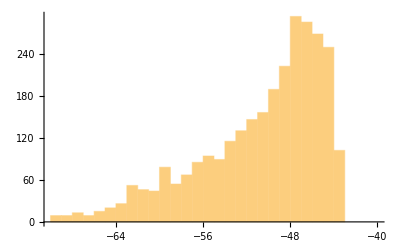

```mathematica
Histogram[SortedLikelihoods⟦All,3⟧,{-70,-40,1}]
```

```mathematica
TableOfLikelihoods⟦1,1,3⟧
```

-68.0721

```mathematica
TableOfLikelihoods⟦20,20,3⟧
```

-45.1518

```mathematica
MostLikely⟦3⟧
```

-43.5605

```mathematica
Min[TableOfLikelihoods⟦All,All,3⟧-MostLikely⟦3⟧]
```

-956.44

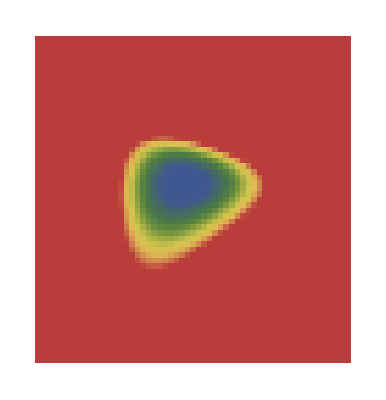

```mathematica
ArrayPlot[TableOfLikelihoods⟦All,All,3⟧-MostLikely⟦3⟧,ColorFunctionScaling->False,ColorFunction->(ColorData["DarkRainbow"][-#/2]&)]
```

```mathematica
SortedLikelihoods⟦1⟧
```

{14.,1.5,-43.5605}

## plotting olaparib data

```mathematica
Therapy1Name="Paclitaxel_Carboplatin";
Therapy1FileName="Paclitaxel_Carboplatin_events.csv";

Therapy2Name="Olaparib";
Therapy2FileName="Olaparib_events.csv";


(* please include a header in the source data which specifies the time units (e.g. weeks, or months). The same time units must be used for both therapies *)
Header=Import[NotebookDirectory[]<>Therapy1FileName,"CSV"]⟦1,1⟧
```

Time (months)

#### importing event data

```mathematica
Therapy1EventFile=Import[NotebookDirectory[]<>Therapy1FileName,"CSV"]⟦2;;⟧;
Therapy2EventFile=Import[NotebookDirectory[]<>Therapy2FileName,"CSV"]⟦2;;⟧;
```

```mathematica
Therapy1LongestEvent=Max[Therapy1EventFile⟦All,1⟧]
Therapy2LongestEvent=Max[Therapy2EventFile⟦All,1⟧]
SharedTimeFrame=Min[{Therapy1LongestEvent,Therapy2LongestEvent}]
```

19.1

24.7

19.1

### Plotting trial data

```mathematica
Therapy1Color=RGBColor[0.5,0.7,0];
Therapy2Color=RGBColor[0.8,0.1,0.6];

Therapy1Events=EventData[Therapy1EventFile⟦All,1⟧,Therapy1EventFile⟦All,2⟧];
Therapy2Events=EventData[Therapy2EventFile⟦All,1⟧,Therapy2EventFile⟦All,2⟧];

Therapy1SurvivalModelFit[t_]:=SurvivalModelFit[Therapy1Events][t]
Therapy2SurvivalModelFit[t_]:=SurvivalModelFit[Therapy2Events][t]

Therapy1CensoredEvents=Cases[Transpose[{Therapy1Events["CensoredData"],Therapy1Events["CensoringIndicators"]}],{_,1}];
Therapy2CensoredEvents=Cases[Transpose[{Therapy2Events["CensoredData"],Therapy2Events["CensoringIndicators"]}],{_,1}];

Therapy1CensorGraphics=Graphics[Join[{AbsoluteThickness[1],Darker[Therapy1Color,0.3]},Table[Line[{{i,Therapy1SurvivalModelFit[i]-.04},{i,Therapy1SurvivalModelFit[i]+.04}}],{i,Therapy1CensoredEvents⟦All,1⟧}]]];
Therapy2CensorGraphics=Graphics[Join[{AbsoluteThickness[1],Darker[Therapy2Color,0.3]},Table[Line[{{i,Therapy2SurvivalModelFit[i]-.04},{i,Therapy2SurvivalModelFit[i]+.04}}],{i,Therapy2CensoredEvents⟦All,1⟧}]]];
```

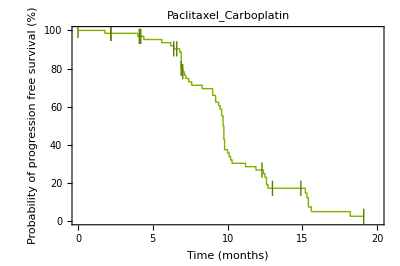

```mathematica
Therapy1Plot=Show[
Plot[SurvivalFunction[EmpiricalDistribution[Therapy1Events]][x],{x,0,Therapy1LongestEvent},Exclusions->None,PlotRange->{{0,Therapy1LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotLabel->Therapy1Name,PlotStyle->Directive[AbsoluteThickness[1],Therapy1Color]]
,
Therapy1CensorGraphics
]
```

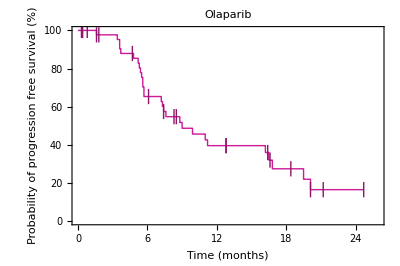

```mathematica
Therapy2Plot=Show[
Plot[SurvivalFunction[EmpiricalDistribution[Therapy2Events]][x],{x,0,Therapy2LongestEvent},Exclusions->None,PlotRange->{{0,Therapy2LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotLabel->Therapy2Name,PlotStyle->Directive[AbsoluteThickness[1],Therapy2Color]]
,
Therapy2CensorGraphics
]
```

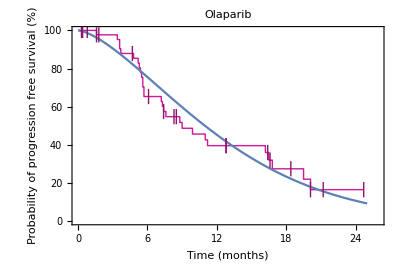

```mathematica
Show[
Plot[SurvivalFunction[EmpiricalDistribution[Therapy2Events]][x],{x,0,Therapy2LongestEvent},Exclusions->None,PlotRange->{{0,Therapy2LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotLabel->Therapy2Name,PlotStyle->Directive[AbsoluteThickness[1],Therapy2Color]]
,
Plot[MySurvivalFunction[SortedLikelihoods⟦1,1⟧,SortedLikelihoods⟦1,2⟧,t],{t,0,25},PlotRange->{{0,25},{0,1}}]
,
Therapy2CensorGraphics
]
```

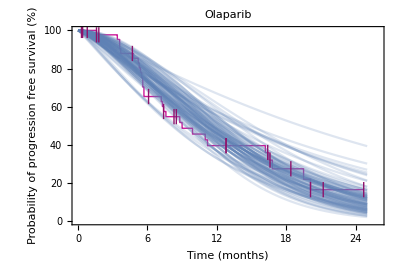

```mathematica
(*95% confidence interval
 RandomChoice[10^SortedLikelihoods[[All, 3]]->SortedLikelihoods]
*)

Model1=Table[RandomChoice[10^SortedLikelihoods[[All, 3]]->SortedLikelihoods],{i,1,100} ]; 
(*SortedLikelihoods=Sort[Flatten[Model1,1],#1⟦3⟧>#2⟦3⟧&];*)
Model1=Sort[Model1,#1[[3]]<#2[[3]]&];
Show[
Plot[SurvivalFunction[EmpiricalDistribution[Therapy2Events]][x],{x,0,Therapy2LongestEvent},Exclusions->None,PlotRange->{{0,Therapy2LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotLabel->Therapy2Name,PlotStyle->Directive[AbsoluteThickness[1],Therapy2Color]]
,
Plot[Table[MySurvivalFunction[Model1⟦i,1⟧,Model1⟦i,2⟧,t],{i,1,95}],{t,0,25},PlotRange->{{0,25},{0,1}},PlotStyle->Opacity[0.2]]
,
Therapy2CensorGraphics
]
```

```mathematica
parameterset=56;
MySurvivalFunction[Model1⟦parameterset,1⟧,Model1⟦parameterset,2⟧,14.534]
```

0.366759

```mathematica
ChemotherapySurvivalFunction=SurvivalFunction[EmpiricalDistribution[Therapy1Events]]
```

Function[{x$},SurvivalFunction[DataDistribution[…],x$],Listable]

```mathematica
ChemotherapySurvivalFunction[14.423]
```

0.17169

```mathematica
PredictedCombinationTherapy[parameterset_,t_,ρ_]:=Max[{
ChemotherapySurvivalFunction[t]+(1-ChemotherapySurvivalFunction[t])*MySurvivalFunction[Model1⟦parameterset,1⟧,Model1⟦parameterset,2⟧,t]*(1-ρ),
MySurvivalFunction[Model1⟦parameterset,1⟧,Model1⟦parameterset,2⟧,t]+(1-MySurvivalFunction[Model1⟦parameterset,1⟧,Model1⟦parameterset,2⟧,t])*ChemotherapySurvivalFunction[t]*(1-ρ)
}]
```

```mathematica
PredictedCombinationTherapy[10,12.232,0.3]
```

0.446484

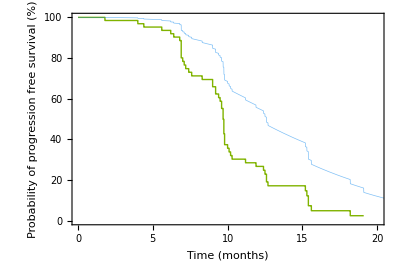

```mathematica
Show[
Plot[ChemotherapySurvivalFunction[x],{x,0,Therapy1LongestEvent},Exclusions->None,PlotRange->{{0,Therapy1LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotStyle->Directive[AbsoluteThickness[1],Therapy1Color]]
,
Plot[PredictedCombinationTherapy[50,t,0.],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[0.5],AbsoluteThickness[0.5]]]
]
```

```mathematica
(*plotpoints*) pp=2;
(* opacity *)op=0.2;

Models10=Plot[Table[PredictedCombinationTherapy[i,t,0.],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
```

```mathematica
(*plotpoints*) pp=2;

Models10=Plot[Table[PredictedCombinationTherapy[i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models20=Plot[Table[PredictedCombinationTherapy[10+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models30=Plot[Table[PredictedCombinationTherapy[20+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models40=Plot[Table[PredictedCombinationTherapy[30+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models50=Plot[Table[PredictedCombinationTherapy[40+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models60=Plot[Table[PredictedCombinationTherapy[50+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models70=Plot[Table[PredictedCombinationTherapy[60+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models80=Plot[Table[PredictedCombinationTherapy[70+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
Models90=Plot[Table[PredictedCombinationTherapy[80+i,t,0.3],{i,1,10}],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None,PlotStyle->Directive[ColorData[3,6],Opacity[op],AbsoluteThickness[0.5]],PlotPoints->pp];
```

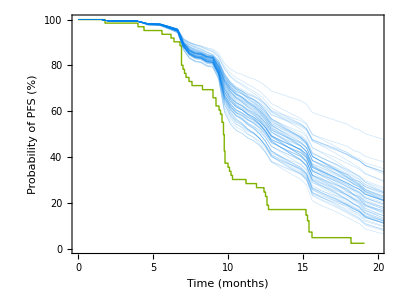

```mathematica
PredictionFigure=Show[
Plot[ChemotherapySurvivalFunction[x],{x,0,Therapy1LongestEvent},Exclusions->None,PlotRange->{{0,20(*Therapy1LongestEvent*1.05*)},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of PFS (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->3/4,ImageSize->{{500},{180}},ImagePadding->{{75,10},{50,10}},FrameTicks->{{Table[{i,100*i,{0,0.02}},{i,0,1,2/10}],None},{Table[{i,i,{0,0.02}},{i,0,20,5}],None}},PlotStyle->Directive[AbsoluteThickness[1],Therapy1Color]]
,
Models10,Models20,Models30,Models40,Models50,Models60,Models70
]
```

```mathematica
Export[NotebookDirectory[]<>"Ensemble of predictions.pdf",PredictionFigure,"PDF"]
Export[NotebookDirectory[]<>"Ensemble of predictions.png",PredictionFigure,"PNG",ImageResolution->600]
```

D:\Dropbox\_Grants\Cancer Research Institute Technology Impact Award\fitting events to log normal\Ensemble of predictions.pdf

D:\Dropbox\_Grants\Cancer Research Institute Technology Impact Award\fitting events to log normal\Ensemble of predictions.png

# OLD

```mathematica
Show[
Plot[ChemotherapySurvivalFunction[x],{x,0,Therapy1LongestEvent},Exclusions->None,PlotRange->{{0,Therapy1LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotLabel->Therapy1Name,PlotStyle->Directive[AbsoluteThickness[1],Therapy1Color]]
,
Plot[PredictedCombinationTherapy[50,t,0.],{t,0,25},PlotRange->{{0,25},{0,1}},Exclusions->None]
,
Therapy1CensorGraphics
]
```

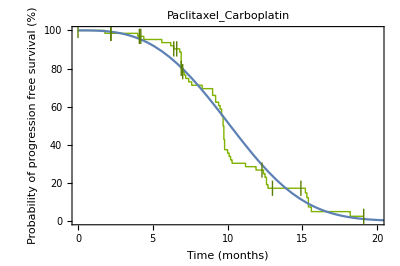

```mathematica
Show[
Plot[SurvivalFunction[EmpiricalDistribution[Therapy1Events]][x],{x,0,Therapy1LongestEvent},Exclusions->None,PlotRange->{{0,Therapy1LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotLabel->Therapy1Name,PlotStyle->Directive[AbsoluteThickness[1],Therapy1Color]]
,
Plot[MySurvivalFunction[SortedLikelihoodsChemotherapy⟦1,1⟧,SortedLikelihoodsChemotherapy⟦1,2⟧,t],{t,0,25},PlotRange->{{0,25},{0,1}}]
,
Therapy1CensorGraphics
]
```

General::munfl: 1/10^314.321 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

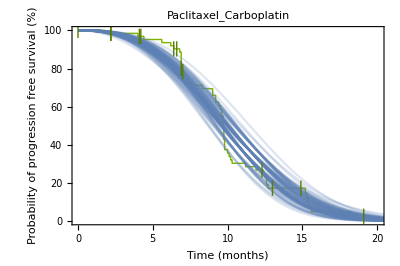

```mathematica
Model2=Table[RandomChoice[10^SortedLikelihoodsChemotherapy[[All, 3]]->SortedLikelihoodsChemotherapy],{i,1,100} ];
Model2=Sort[Model2,#1[[3]]<#2[[3]]&]; 
Show[
Plot[SurvivalFunction[EmpiricalDistribution[Therapy1Events]][x],{x,0,Therapy1LongestEvent},Exclusions->None,PlotRange->{{0,Therapy1LongestEvent*1.05},{0,1}},PlotPoints->500,Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Header,"Probability of\nprogression free survival (%)"},PlotRangePadding->None,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Thickness[Medium],Black],AspectRatio->2/3,ImageSize->{{1000},{270}},ImagePadding->{{80,10},{60,10}},FrameTicks->{{Table[{i,100*i,{0.015,0}},{i,0,1,2/10}],None},{Automatic,None}},PlotLabel->Therapy1Name,PlotStyle->Directive[AbsoluteThickness[1],Therapy1Color]]
,
Plot[Table[MySurvivalFunction[Model2⟦i,1⟧,Model2⟦i,2⟧,t],{i,1,95}],{t,0,25},PlotRange->{{0,25},{0,1}},PlotStyle->Opacity[0.2]]
,
Therapy1CensorGraphics
]
```

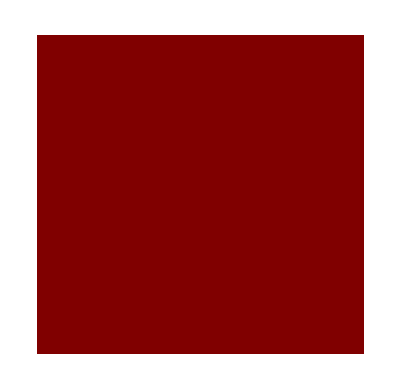

```mathematica
ArrayPlot[TableOfLikelihoods⟦All,All,3⟧-MostLikely⟦3⟧,ColorFunctionScaling->False,ColorFunction->(ColorData["DarkRainbow"][-#/2]&)
PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"metres"],Below]}]
```

## Plotting residuals for log normal distribution with best fit to olaparib individual patient data

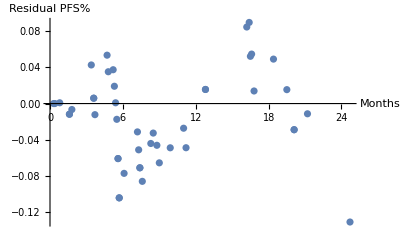

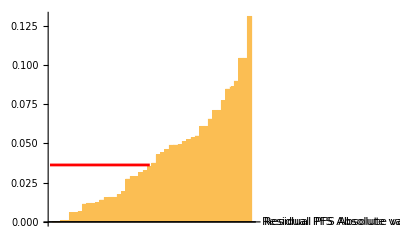

Median absolute residual PFS: 0.0362848 Max absolute residual PFS: 0.130933

```mathematica
EventTimesOlaparib= Therapy2EventFile⟦All,1⟧;
LogNormalFitEvents= MySurvivalFunction[SortedLikelihoods⟦1,1⟧,SortedLikelihoods⟦1,2⟧,EventTimesOlaparib];
OlaparibData= SurvivalFunction[EmpiricalDistribution[Therapy2Events],EventTimesOlaparib];
(*Show[ListPlot[LogNormalFitEvents], ListPlot[OlaparibData ]]*)

(*Plot residuals for optimal fit as found by Mathematica function versus our method, Mathematica method values the stuff at the beginnig just as much as the stuff towards the end, so estimates are not identical*)
Residuals= OlaparibData-LogNormalFitEvents; 
MedianResidual= Median[Abs[OlaparibData-LogNormalFitEvents]];
MaxResidual= Max[Abs[OlaparibData-LogNormalFitEvents]];
Show[ListPlot[Transpose[{EventTimesOlaparib,Residuals}]],  AxesLabel-> {"Months","Residual PFS%" }]
BarChart[Sort[Abs[OlaparibData-LogNormalFitEvents]], AxesLabel-> {"Residual PFS Absolute value"}, Epilog->{Red,AbsoluteThickness[2],Line[{{0, MedianResidual},{Length[Residuals]*0.5, MedianResidual}}]}]
Print["Median absolute residual PFS: ", MedianResidual, " Max absolute residual PFS: " ,   MaxResidual]
```

## Plotting residuals for log normal distribution with best fit to Paclitaxel and Carboplatin individual patient data

{9.5,0.175}

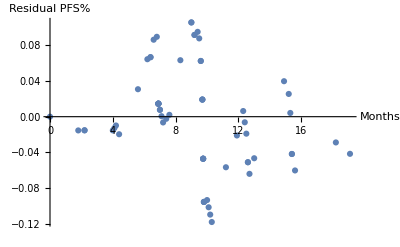

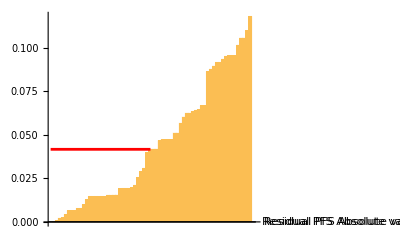

Median absolute residual PFS 0.0416218, Max absolute residual PFS 0.117803

```mathematica
(*Corrected so that residuals are claculated for every event*)
EventTimesChemo= Therapy1EventFile⟦All,1⟧;
LogNormalFitEventsChemo= MySurvivalFunction[SortedLikelihoodsChemotherapy⟦1,1⟧,SortedLikelihoodsChemotherapy⟦1,2⟧,EventTimesChemo];
ChemoData= SurvivalFunction[EmpiricalDistribution[Therapy1Events],EventTimesChemo];
{EstimatedMean=SortedLikelihoodsChemotherapy⟦1,1⟧, EstimaredStdev=SortedLikelihoodsChemotherapy⟦1,2⟧}
(*Plot residuals for optimal fit as found by Mathematica function versus our method, Mathematica method values the stuff at the beginnig just as much as the stuff towards the end, so estimates are not identical*)

Residuals= ChemoData-LogNormalFitEventsChemo; 
MedianResidual=Median[Abs[ChemoData-LogNormalFitEventsChemo]];
Show[ListPlot[Transpose[{EventTimesChemo,Residuals}]],  AxesLabel-> {"Months","Residual PFS%" }]
BarChart[Sort[Abs[ChemoData-LogNormalFitEventsChemo]], AxesLabel-> {"Residual PFS Absolute value"} , Epilog->{Red,AbsoluteThickness[2],Line[{{0, MedianResidual},{Length[Residuals]*0.5, MedianResidual}}]}]
Print["Median absolute residual PFS ",MedianResidual, ", Max absolute residual PFS " ,   Max[Abs[ChemoData-LogNormalFitEventsChemo]]]
```

## Sampling from likely log normal distributions for each monotherapy to perform head to head comparison

```mathematica
(*Performed weighted sampling from each of the distributions*)
NumberofDistributionstoSample=10000;
OlaparibWeightedSample= RandomChoice[10^SortedLikelihoods[[All, 3]]->SortedLikelihoods,NumberofDistributionstoSample];
ChemoWeightedSample= RandomChoice[10^SortedLikelihoodsChemotherapy[[All, 3]]->SortedLikelihoodsChemotherapy,NumberofDistributionstoSample]; 
(*Pickimg 50 people from 1 distribution*)
ComparisonCounts=0 ;
ResultsSimulatedTrialOlaparib=Table[MySurvivalFunctionInverse[OlaparibWeightedSample[[1, 1]],OlaparibWeightedSample[[1, 2]],1-RandomReal[]],50];
AveragePFSSimulated=Mean[ResultsSimulatedTrialOlaparib];
ResultsSimulatedTrialChemo=Table[MySurvivalFunctionInverse[ChemoWeightedSample[[1, 1]],ChemoWeightedSample[[1, 2]],1-RandomReal[]],50];
AveragePFSSimulatedChemo=Mean[ResultsSimulatedTrialChemo];
If[AveragePFSSimulated>AveragePFSSimulatedChemo,ComparisonCounts=ComparisonCounts=+1;]
```

```mathematica
(*Doing this 1000 times*)
ComparisonCounts=0 ;
For[i=1, i≤NumberofDistributionstoSample, i++,
ResultsSimulatedTrialOlaparib=Table[MySurvivalFunctionInverse[OlaparibWeightedSample[[i, 1]],OlaparibWeightedSample[[i, 2]],1-RandomReal[]],50];
AveragePFSSimulated=Mean[ResultsSimulatedTrialOlaparib];
ResultsSimulatedTrialChemo=Table[MySurvivalFunctionInverse[ChemoWeightedSample[[i, 1]],ChemoWeightedSample[[i, 2]],1-RandomReal[]],50];
AveragePFSSimulatedChemo=Mean[ResultsSimulatedTrialChemo];
If[AveragePFSSimulated>AveragePFSSimulatedChemo,ComparisonCounts=ComparisonCounts+1;]
]

N[ComparisonCounts/NumberofDistributionstoSample]
```

0.9273

```mathematica
0.935
Therapy1Color=RGBColor[0.5,0.7,0];
Therapy2Color=RGBColor[0.8,0.1,0.6];
```

0.935

```mathematica
PairedHistogram[ResultsSimulatedTrialOlaparib,ResultsSimulatedTrialChemo, ChartStyle->RGBColor[0.5,0.7,0]]
PairedHistogram[ResultsSimulatedTrialOlaparib,ResultsSimulatedTrialChemo, ChartStyle->RGBColor[0.8,0.1,0.6]]
```

-Graphics-

-Graphics-

```mathematica
(*Doing this 1000 times and printing out the mean difference between treatments*)
TableofDifferences= {}; 
ComparisonCounts=0 ;
For[i=1, i≤NumberofDistributionstoSample, i++,
ResultsSimulatedTrialOlaparib=Table[MySurvivalFunctionInverse[OlaparibWeightedSample[[i, 1]],OlaparibWeightedSample[[i, 2]],1-RandomReal[]],50];
AveragePFSSimulated=Mean[ResultsSimulatedTrialOlaparib];
ResultsSimulatedTrialChemo=Table[MySurvivalFunctionInverse[ChemoWeightedSample[[i, 1]],ChemoWeightedSample[[i, 2]],1-RandomReal[]],50];
AveragePFSSimulatedChemo=Mean[ResultsSimulatedTrialChemo];
MeanDifference=AveragePFSSimulated-AveragePFSSimulatedChemo;
TableofDifferences= {TableofDifferences, MeanDifference};
If[AveragePFSSimulated>AveragePFSSimulatedChemo,ComparisonCounts=ComparisonCounts+1;]; 
]; 
Print["Proportion of time that Olaparib was superior to chemotherapy regime: ", N[ComparisonCounts/NumberofDistributionstoSample], 
"\n Average difference in PFS months between treatments: ",   Mean[Flatten[TableofDifferences]]]
```

Proportion of time that Olaparib was superior to chemotherapy regime: 0.9247
 Average difference in PFS months between treatments: 5.02007

```mathematica
MergedEventData[]
```

EventData::espec: The argument {} is not a valid event specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression EventData[SimulatedTrialsChemo[],{}] cannot be used as a part specification.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression EventData[SimulatedTrialsChemo[],{}] cannot be used as a part specification.

EventData[EventData[{},{}]⟦2,1,EventData[SimulatedTrialsChemo[],{}],2,1⟧,EventData[{},{}]⟦2,2,EventData[SimulatedTrialsChemo[],{}],2,2⟧]

```mathematica
(*Computing hazard ratio*)
CensoringTime=18(* months *);
PatientsPerArmOfSimulatedTrial=1000;
```

```mathematica
SimulatedTrialsOlaparib[]:=
Module[{},  Model1=RandomChoice[10^SortedLikelihoods[[All, 3]]->SortedLikelihoods];
Table[MySurvivalFunctionInverse[Model1⟦1⟧,Model1⟦2⟧,1-RandomReal[]] , PatientsPerArmOfSimulatedTrial]];

SimulatedTrialsOlaparib[]:= Module[{}, 
Model1=RandomChoice[10^SortedLikelihoodsChemotherapy[[All, 3]]->SortedLikelihoodsChemotherapy]; 
Table[MySurvivalFunctionInverse[Model1⟦1⟧,Model1⟦2⟧,1-RandomReal[]] , PatientsPerArmOfSimulatedTrial]];



GenerateCensoredEventData[PatientResponses_,CensoringTime_]:=Module[{ResponsesShorterThanCensoringTime,ResponsesLongerThanCensoringTime},
ResponsesShorterThanCensoringTime=Select[PatientResponses,#≤CensoringTime&];
ResponsesLongerThanCensoringTime=Select[PatientResponses,#>CensoringTime&];
EventData[Join[ResponsesShorterThanCensoringTime,ResponsesLongerThanCensoringTime],Join[Table[0,{Length[ResponsesShorterThanCensoringTime]}],Table[1,{Length[ResponsesLongerThanCensoringTime]}]]]
]

Drug1SimulatedEventData[]:=GenerateCensoredEventData[SimulatedTrialsOlaparib[],CensoringTime]; 
Drug2SimulatedEventData[]:=GenerateCensoredEventData[SimulatedTrialsChemo[],CensoringTime]; 

JoinEventData[EventData1_,EventData2_]:=EventData[Join[EventData1⟦2,1⟧,EventData2⟦2,1⟧],Join[EventData1⟦2,2⟧,EventData2⟦2,2⟧]]

MergedEventData[]:=JoinEventData[Drug1SimulatedEventData[],Drug2SimulatedEventData[]];
Descriptors[]:=Join[Table["Drug 1",{PatientsPerArmOfSimulatedTrial}],Table["Drug 2",{PatientsPerArmOfSimulatedTrial}]];

MergedEventData[]:=JoinEventData[Drug1SimulatedEventData[],Drug2SimulatedEventData[]];
Descriptors[]:=Join[Table["Drug 1",{PatientsPerArmOfSimulatedTrial}],Table["Drug 2",{PatientsPerArmOfSimulatedTrial}]];

(* custom function to join two sets of event data - this is necessary to implement the Cox Proportional Hazards model *)
```

```mathematica
(*NumberOfReplicateTrials=100;*)

(* this function returns the relative risk, and confidence interval, in the format:
(95% lower confidence interval, median estimate, 95% upper confidence interval )
*)
RelativeRiskCalculation[descriptors_,eventdata_,PrintTable_(* set to 1 to print to screen the statistical table of Cox Model output; set to 0 to not show output *)]:=Module[{},
MyModelFit=CoxModelFit[{descriptors,eventdata},{treatment},{treatment},NominalVariables->treatment];

If[PrintTable==1,Print[MyModelFit["ParameterTable"]]];

RelativeRisk=MyModelFit["RelativeRisk"]⟦1⟧;
RelativeRiskLowerConfidenceInterval=MyModelFit["RelativeRiskConfidenceIntervals"]⟦1,1⟧;
RelativeRiskUpperConfidenceInterval=MyModelFit["RelativeRiskConfidenceIntervals"]⟦1,2⟧;

{RelativeRiskLowerConfidenceInterval,RelativeRisk,RelativeRiskUpperConfidenceInterval}
]
HazardRatioRange=Quiet@Mean[Table[RelativeRiskCalculation[Descriptors[],MergedEventData[],0],{NumberOfReplicateTrials}]]
```

$Aborted[]

```mathematica
(*Plotting hazard ratios of all hypothetical combinations
MelanomaAllCombinationsHazardRatios=Flatten[Table[Table[{i,j,AllMelanomaPairs⟦i,j,-1⟧},{i,1,j-1}],{j,2,Length[AllMelanomaPairs]}],1];
NSCLCAllCombinationsHazardRatios=Flatten[Table[Table[{i,j,AllNSCLCPairs⟦i,j,-1⟧},{i,1,j-1}],{j,2,Length[AllNSCLCPairs]}],1];
PDACAllCombinationsHazardRatios=Flatten[Table[Table[{i,j,AllPDACPairs⟦i,j,-1⟧},{i,1,j-1}],{j,2,Length[AllPDACPairs]}],1];
CRCAllCombinationsHazardRatios=Flatten[Table[Table[{i,j,AllCRCPairs⟦i,j,-1⟧},{i,1,j-1}],{j,2,Length[AllCRCPairs]}],1];
BCAllCombinationsHazardRatios=Flatten[Table[(*For each predicted combination,the P-value for a significant improvement in hazard ratio (by Cox proportional hazards model) is closely related to the hazard ratio.We fit a function to this relationship,in order to color the histogram of hazard ratio by the approximate Pvalue of the predictions in each'bin' of hazard ratios*)QuadraticFit=FindFit Select[{AllCombinationsHazardRatios⟦All,3,1⟧,-Log[10,AllCombinationsHazardRatios⟦All,3,2⟧]}ᵀ,#⟦1⟧<1&],a*x2+b*x+c,{a,b,c},x;
Show ListPlot[{AllCombinationsHazardRatios⟦All,3,1⟧,-Log[10,AllCombinationsHazardRatios⟦All,3,2⟧]}ᵀ,PlotRange->{{0.5,1},{0,1.4}},Frame->True,FrameLabel->{"Hazard ratio (combination vs. best monotherapy)","-Log10 P for improvement in hazard ratio"},PlotStyle->Directive[Red,AbsolutePointSize[3]],FrameStyle->Directive[Black,Thickness[Medium]],BaseStyle->{FontFamily->"Arial",FontSize->12},AspectRatio->3/4,ImageSize->{{1000},{250}}],Plota*x2+b*x+c/.QuadraticFit,{x,0,5},PlotStyle->Gray  0.5 0.6 0.7 0.8 0.9 1.0 0.0 0.2 0.4 0.6 0.8 1.0 1.2 1.4 Hazard ratio (combination vs.best monotherapy)-Log10 P for improvement in hazard ratio PDX analysis code.nb 107
(*defining a custom color scale*) Unprotect[ColorData];
ColorData["PValue"]=Function[x,Blend[Transpose[{{0,0.025,0.05,0.1,0.2,0.275,0.325,1.0},{Blend[{Orange,Yellow},0.85],Blend[{Orange,Yellow},0.85],Blend[{Orange,Yellow},0.5],Red,Darker[Red,0.3],Darker[Red,0.6],GrayLevel[0.1],GrayLevel[0.1]}}],x]];
Protect[ColorData];
(*this function allows each bar in the histogram to be colored according to the Pvalue of the combinations in that bar*)CustomChartElementFunction[{{xmin_,xmax_},{ymin_,ymax_}},___]:=ColorData["PValue"] Ifxmax>1,1,10^-a*(xmin/2+xmax/2)2+b*(xmin/2+xmax/2)+c/.QuadraticFit,Dynamic@EdgeForm[None],Rectangle[{xmin,ymin},{xmax,ymax},RoundingRadius->0]
(*plotting a histogram of hazard ratios*) HRHistogram=Histogram[Map[Min[{#,2.5}]&,AllCombinationsHazardRatios⟦All,3,1⟧],{0.0,2.55,0.05},PlotRange->{{0,2.55},{0,All}},PlotRangePadding->None,Axes->False,Frame->{{True,False},{True,False}},ChartElementFunction->CustomChartElementFunction,FrameStyle->Directive[Black,Thickness[Medium]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameTicks->{Append[Table[{i,NumberForm[i,{2,1}],{0,0.015}},{i,0,2,0.5}],{2.5,"2.5+",{0,0.015}}],Table[{i,i,{0,0.015}},{i,0,100,10}]},FrameLabel->{"Hazard Ratio (combination vs. best monotherapy)","Number of combinations"},ImagePadding->{{50,10},{50,10}},AspectRatio->3/5,ImageSize->{{1000},{220}}] Export[NotebookDirectory[]<>"Figure 5A, Hazard ratio of predicted combinations.pdf",HRHistogram,"PDF"];
0.0 0.5 1.0 1.5 2.0 2.5+0 10 20 30 40 50 Hazard Ratio (combination vs.best monotherapy) Number of combinations 108 PDX analysis code.nb HRHistogramZoom=Histogram[Map[Min[{#,2.5}]&,AllCombinationsHazardRatios⟦All,3,1⟧],{0.5,1.0-4*0.05,0.05},PlotRange->{{0.575,0.8},{0,11.3}},PlotRangePadding->None,Axes->False,Frame->{{True,False},{True,False}},ChartElementFunction->CustomChartElementFunction,FrameStyle->Directive[Black,Thickness[Medium]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameTicks->{Table[{i,NumberForm[i,{2,1}],{0,0.05}},{i,0,2,0.1}],Join[Table[{i,i,{0,0.05}},{i,0,30,5}],Table[{i, ,{0,0.03}},{i,0,30,1}]]},FrameLabel->{"","Number of combinations"},ImagePadding->{{50,10},{50,10}},AspectRatio->2,ImageSize->{{1000},{220}},Epilog->(*this is a white sinusoid over the top of the highest bar to indicate that the vertical scale is truncated*){White,Polygon[Append[Prepend[Table[{0.7+Θ/(6.4 Π)*0.1,11+0.14*Sin[Θ]},{Θ,0,6.4 Π,0.2}],{0.7,13}],{0.8,13}]]}] Export[NotebookDirectory[]<>"Figure 5A, zoomed.pdf",HRHistogramZoom,"PDF"];
0.6 0.7 0.8 0 5 10 Number of combinations
(*color scale*) HRHistogramColorScale=ContourPlot[y,{x,0,1},{y,0,0.5},ColorFunction->(ColorData["PValue"][#]&),ColorFunctionScaling->False,Contours->50,ContourStyle->None,PlotRangePadding->None,AspectRatio->10,FrameTicks->{{Table[{i,NumberForm[i,{2,1}],{0,0.25}},{i,0,0.5,0.1}],None},{None,None}},FrameStyle->Directive[Black,Thickness[Medium]],BaseStyle->{FontFamily->"Arial",FontSize->12},ImagePadding->{{100,5},{10,10}},ImageSize->{{500},{160}},FrameLabel->{,"P-value for Hazard Ratio <1"},PerformanceGoal->"Speed"]/.({EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___} ⧴ {EdgeForm[r],r,i}) Export[NotebookDirectory[]<>"Figure 5A, color scale.pdf",HRHistogramColorScale,"PDF"];*)
0.0 0.1 0.2 0.3 0.4 0.5 P-value for Hazard Ratio<1 I
```

Less::nord: Invalid comparison with ⅈ attempted.

0.-for Hazard Ratio value<ⅈ